## Probability - obtained using Minakata expansion

## Case ϵ_μτ!=0

```mathematica
(* the formula is expanded up to order 3/2 *)

(* In the formula below, we have a=(ρ/(3.0g/cm^3))*1/(3 500 km)  *)

(* Δm31 and Δm21 are the mass squared diferences in eV^2 *)

(* L is the Length in m *)

(* ee is the energy in GeV *)

(* dcp is the Dirac CP violation phase *)

(* sij is Sin(Subscript[θ, ij]) and cij is Cos(Subscript[θ, ij]) *)

(* emut is the NSI *)
```

```mathematica
pmut[s12_,c12_,s13_,c13_,s23_,c23_,dcp_,dm31_,dm21_,ee_,a_,emut_]=(1.5120486057984994*^-27 a^3 c23^2 dm31 ee s23^2-7.77701383771046*^-14 a^2 c23^2 dm31^2 ee s23^2+a c23^2 dm31^3 ee s23^2+8.165062471311897*^-26 a^3 c23 dm31 ee emut s23^3-4.199587472363649*^-12 a^2 c23 dm31^2 ee emut s23^3+54. a c23 dm31^3 ee emut s23^3+1.102283433627106*^-24 a^3 dm31 ee emut^2 s23^4-5.6694430876909255*^-11 a^2 dm31^2 ee emut^2 s23^4+729. a dm31^3 ee emut^2 s23^4-3.0240972115969988*^-27 a^3 c12 c23^3 dm21 ee s12 s13 s23 Cos[dcp]+1.555402767542092*^-13 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Cos[dcp]-2. a c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[dcp]-2.449518741393569*^-25 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Cos[dcp]+1.049896868090912*^-11 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[dcp]-54. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[dcp]-1.3887078286566998*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Cos[dcp]+3.0240972115969988*^-27 a^3 c12 c23 dm21 ee s12 s13 s23^3 Cos[dcp]-7.77701383771046*^-14 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Cos[dcp]-2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[dcp]+5.143362328358147*^13 c12 c23 dm21 dm31^3 ee s12 s13 s23^3 Cos[dcp]-4.409133734508424*^-24 a^3 c12 c23 dm21 ee emut^2 s12 s13 s23^3 Cos[dcp]+1.7008329263072776*^-10 a^2 c12 c23 dm21 dm31 ee emut^2 s12 s13 s23^3 Cos[dcp]-3.749511137373089*^16 c12 c23 dm21 dm31^3 ee emut^2 s12 s13 s23^3 Cos[dcp]+8.165062471311897*^-26 a^3 c12 dm21 ee emut s12 s13 s23^4 Cos[dcp]-2.0997937361818243*^-12 a^2 c12 dm21 dm31 ee emut s12 s13 s23^4 Cos[dcp]-54. a c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[dcp]+1.3887078286566998*^15 c12 dm21 dm31^3 ee emut s12 s13 s23^4 Cos[dcp]+8.165062471311897*^-26 a^3 c23^3 dm31 ee emut s23 Cos[(0.002535587291032924 dm31 L)/ee]-4.199587472363649*^-12 a^2 c23^3 dm31^2 ee emut s23 Cos[(0.002535587291032924 dm31 L)/ee]+54. a c23^3 dm31^3 ee emut s23 Cos[(0.002535587291032924 dm31 L)/ee]-54. a c23^3 dm31^3 ee emut s13^2 s23 Cos[(0.002535587291032924 dm31 L)/ee]-3.0240972115969988*^-27 a^3 c23^2 dm31 ee s23^2 Cos[(0.002535587291032924 dm31 L)/ee]+1.555402767542092*^-13 a^2 c23^2 dm31^2 ee s23^2 Cos[(0.002535587291032924 dm31 L)/ee]-2. a c23^2 dm31^3 ee s23^2 Cos[(0.002535587291032924 dm31 L)/ee]+2.204566867254212*^-24 a^3 c23^2 dm31 ee emut^2 s23^2 Cos[(0.002535587291032924 dm31 L)/ee]-1.1338886175381851*^-10 a^2 c23^2 dm31^2 ee emut^2 s23^2 Cos[(0.002535587291032924 dm31 L)/ee]+1458. a c23^2 dm31^3 ee emut^2 s23^2 Cos[(0.002535587291032924 dm31 L)/ee]+2. a c23^2 dm31^3 ee s13^2 s23^2 Cos[(0.002535587291032924 dm31 L)/ee]-1458. a c23^2 dm31^3 ee emut^2 s13^2 s23^2 Cos[(0.002535587291032924 dm31 L)/ee]-8.165062471311897*^-26 a^3 c23 dm31 ee emut s23^3 Cos[(0.002535587291032924 dm31 L)/ee]+4.199587472363649*^-12 a^2 c23 dm31^2 ee emut s23^3 Cos[(0.002535587291032924 dm31 L)/ee]-54. a c23 dm31^3 ee emut s23^3 Cos[(0.002535587291032924 dm31 L)/ee]+54. a c23 dm31^3 ee emut s13^2 s23^3 Cos[(0.002535587291032924 dm31 L)/ee]-8.165062471311897*^-26 a^3 c12 c23^4 dm21 ee emut s12 s13 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+4.199587472363649*^-12 a^2 c12 c23^4 dm21 dm31 ee emut s12 s13 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]-54. a c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+3.0240972115969988*^-27 a^3 c12 c23^3 dm21 ee s12 s13 s23 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]-1.555402767542092*^-13 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+2. a c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]-4.409133734508424*^-24 a^3 c12 c23^3 dm21 ee emut^2 s12 s13 s23 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+1.7008329263072776*^-10 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]-3.749511137373089*^16 c12 c23^3 dm21 dm31^3 ee emut^2 s12 s13 s23 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+2.449518741393569*^-25 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]-8.399174944727297*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]-54. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+2.7774156573133995*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]-3.0240972115969988*^-27 a^3 c12 c23 dm21 ee s12 s13 s23^3 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+7.77701383771046*^-14 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]-5.143362328358147*^13 c12 c23 dm21 dm31^3 ee s12 s13 s23^3 Cos[dcp] Cos[(0.002535587291032924 dm31 L)/ee]+1.102283433627106*^-24 a^3 c23^4 dm31 ee emut^2 Cos[(0.002535587291032924 dm31 L)/ee]^2-5.6694430876909255*^-11 a^2 c23^4 dm31^2 ee emut^2 Cos[(0.002535587291032924 dm31 L)/ee]^2+729. a c23^4 dm31^3 ee emut^2 Cos[(0.002535587291032924 dm31 L)/ee]^2-1458. a c23^4 dm31^3 ee emut^2 s13^2 Cos[(0.002535587291032924 dm31 L)/ee]^2-8.165062471311897*^-26 a^3 c23^3 dm31 ee emut s23 Cos[(0.002535587291032924 dm31 L)/ee]^2+4.199587472363649*^-12 a^2 c23^3 dm31^2 ee emut s23 Cos[(0.002535587291032924 dm31 L)/ee]^2-54. a c23^3 dm31^3 ee emut s23 Cos[(0.002535587291032924 dm31 L)/ee]^2+108. a c23^3 dm31^3 ee emut s13^2 s23 Cos[(0.002535587291032924 dm31 L)/ee]^2+1.5120486057984994*^-27 a^3 c23^2 dm31 ee s23^2 Cos[(0.002535587291032924 dm31 L)/ee]^2-7.77701383771046*^-14 a^2 c23^2 dm31^2 ee s23^2 Cos[(0.002535587291032924 dm31 L)/ee]^2+a c23^2 dm31^3 ee s23^2 Cos[(0.002535587291032924 dm31 L)/ee]^2-2. a c23^2 dm31^3 ee s13^2 s23^2 Cos[(0.002535587291032924 dm31 L)/ee]^2+a c23 dm31^3 ee s13^2 Cos[(9.859648724542914*^-17 a L)/ee] (s23 (54. c23^2 emut+c23 (-2.+1458. emut^2) s23-54. emut s23^2)+c23 (1458. c23^2 emut^2-108. c23 emut s23+2. s23^2) Cos[(0.002535587291032924 dm31 L)/ee])+2.0997937361818243*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-54. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-7.77701383771046*^-14 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+5.6694430876909255*^-11 a^2 c12 c23 dm21 dm31 ee emut^2 s12 s13 s23^3 Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-1458. a c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-2.0997937361818243*^-12 a^2 c12 dm21 dm31 ee emut s12 s13 s23^4 Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+54. a c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+5.6694430876909255*^-11 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-1458. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-4.199587472363649*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+108. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+7.77701383771046*^-14 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Cos[(0.002535587291032924 dm31 L)/ee] Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(0.002535587291032924 dm31 L)/ee] Cos[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+c12 c23 dm21 dm31^2 ee s12 s13 (s23 (a (-2. c23^2-108. c23 emut s23-1458. emut^2 s23^2)+dm31 (5.143362328358147*^13 c23^2+2.7774156573133995*^15 c23 emut s23+3.749511137373089*^16 emut^2 s23^2))+c23 (dm31 (1.3887078286566998*^15 c23^2 emut+c23 (-5.143362328358147*^13+3.749511137373089*^16 emut^2) s23-1.3887078286566998*^15 emut s23^2)+a (-54. c23^2 emut+c23 (2.-1458. emut^2) s23+54. emut s23^2)) Cos[(0.002535587291032924 dm31 L)/ee]) Cos[dcp-(9.859648724542914*^-17 a L)/ee]-7.77701383771046*^-14 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Cos[dcp+(1.232595164407831*^-32 a L)/ee]+4. a c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[dcp+(1.232595164407831*^-32 a L)/ee]-5.143362328358147*^13 c12 c23^3 dm21 dm31^3 ee s12 s13 s23 Cos[dcp+(1.232595164407831*^-32 a L)/ee]-4.199587472363649*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[dcp+(1.232595164407831*^-32 a L)/ee]+216. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[dcp+(1.232595164407831*^-32 a L)/ee]-2.7774156573133995*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Cos[dcp+(1.232595164407831*^-32 a L)/ee]-5.6694430876909255*^-11 a^2 c12 c23 dm21 dm31 ee emut^2 s12 s13 s23^3 Cos[dcp+(1.232595164407831*^-32 a L)/ee]+2916. a c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[dcp+(1.232595164407831*^-32 a L)/ee]-3.749511137373089*^16 c12 c23 dm21 dm31^3 ee emut^2 s12 s13 s23^3 Cos[dcp+(1.232595164407831*^-32 a L)/ee]-2.0997937361818243*^-12 a^2 c12 c23^4 dm21 dm31 ee emut s12 s13 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]+108. a c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]-1.3887078286566998*^15 c12 c23^4 dm21 dm31^3 ee emut s12 s13 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]+7.77701383771046*^-14 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]-4. a c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]+5.143362328358147*^13 c12 c23^3 dm21 dm31^3 ee s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]-5.6694430876909255*^-11 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]+2916. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]-3.749511137373089*^16 c12 c23^3 dm21 dm31^3 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]+2.0997937361818243*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]-108. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]+1.3887078286566998*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(1.232595164407831*^-32 a L)/ee]-54. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[dcp+(9.859648724542914*^-17 a L)/ee]+1.3887078286566998*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Cos[dcp+(9.859648724542914*^-17 a L)/ee]+2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[dcp+(9.859648724542914*^-17 a L)/ee]-5.143362328358147*^13 c12 c23 dm21 dm31^3 ee s12 s13 s23^3 Cos[dcp+(9.859648724542914*^-17 a L)/ee]-1458. a c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[dcp+(9.859648724542914*^-17 a L)/ee]+3.749511137373089*^16 c12 c23 dm21 dm31^3 ee emut^2 s12 s13 s23^3 Cos[dcp+(9.859648724542914*^-17 a L)/ee]+54. a c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[dcp+(9.859648724542914*^-17 a L)/ee]-1.3887078286566998*^15 c12 dm21 dm31^3 ee emut s12 s13 s23^4 Cos[dcp+(9.859648724542914*^-17 a L)/ee]-1458. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(9.859648724542914*^-17 a L)/ee]+3.749511137373089*^16 c12 c23^3 dm21 dm31^3 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(9.859648724542914*^-17 a L)/ee]+108. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(9.859648724542914*^-17 a L)/ee]-2.7774156573133995*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(9.859648724542914*^-17 a L)/ee]-2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(9.859648724542914*^-17 a L)/ee]+5.143362328358147*^13 c12 c23 dm21 dm31^3 ee s12 s13 s23^3 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(9.859648724542914*^-17 a L)/ee]+3.0240972115969988*^-27 a^3 c12 c23^3 dm21 ee s12 s13 s23 Cos[dcp-(0.002535587291032924 dm31 L)/ee]-7.77701383771046*^-14 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Cos[dcp-(0.002535587291032924 dm31 L)/ee]+1.6330124942623794*^-25 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Cos[dcp-(0.002535587291032924 dm31 L)/ee]-4.199587472363649*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[dcp-(0.002535587291032924 dm31 L)/ee]+2.204566867254212*^-24 a^3 c12 c23 dm21 ee emut^2 s12 s13 s23^3 Cos[dcp-(0.002535587291032924 dm31 L)/ee]-5.6694430876909255*^-11 a^2 c12 c23 dm21 dm31 ee emut^2 s12 s13 s23^3 Cos[dcp-(0.002535587291032924 dm31 L)/ee]+8.165062471311897*^-26 a^3 c12 c23^4 dm21 ee emut s12 s13 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp-(0.002535587291032924 dm31 L)/ee]-2.0997937361818243*^-12 a^2 c12 c23^4 dm21 dm31 ee emut s12 s13 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp-(0.002535587291032924 dm31 L)/ee]-3.0240972115969988*^-27 a^3 c12 c23^3 dm21 ee s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp-(0.002535587291032924 dm31 L)/ee]+7.77701383771046*^-14 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp-(0.002535587291032924 dm31 L)/ee]+2.204566867254212*^-24 a^3 c12 c23^3 dm21 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp-(0.002535587291032924 dm31 L)/ee]-5.6694430876909255*^-11 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp-(0.002535587291032924 dm31 L)/ee]-8.165062471311897*^-26 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp-(0.002535587291032924 dm31 L)/ee]+2.0997937361818243*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp-(0.002535587291032924 dm31 L)/ee]+8.165062471311897*^-26 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Cos[dcp+(0.002535587291032924 dm31 L)/ee]-4.199587472363649*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[dcp+(0.002535587291032924 dm31 L)/ee]+54. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[dcp+(0.002535587291032924 dm31 L)/ee]-3.0240972115969988*^-27 a^3 c12 c23 dm21 ee s12 s13 s23^3 Cos[dcp+(0.002535587291032924 dm31 L)/ee]+1.555402767542092*^-13 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Cos[dcp+(0.002535587291032924 dm31 L)/ee]-2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[dcp+(0.002535587291032924 dm31 L)/ee]+2.204566867254212*^-24 a^3 c12 c23 dm21 ee emut^2 s12 s13 s23^3 Cos[dcp+(0.002535587291032924 dm31 L)/ee]-1.1338886175381851*^-10 a^2 c12 c23 dm21 dm31 ee emut^2 s12 s13 s23^3 Cos[dcp+(0.002535587291032924 dm31 L)/ee]+1458. a c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[dcp+(0.002535587291032924 dm31 L)/ee]-8.165062471311897*^-26 a^3 c12 dm21 ee emut s12 s13 s23^4 Cos[dcp+(0.002535587291032924 dm31 L)/ee]+4.199587472363649*^-12 a^2 c12 dm21 dm31 ee emut s12 s13 s23^4 Cos[dcp+(0.002535587291032924 dm31 L)/ee]-54. a c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[dcp+(0.002535587291032924 dm31 L)/ee]+2.204566867254212*^-24 a^3 c12 c23^3 dm21 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]-1.1338886175381851*^-10 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]+1458. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]-1.6330124942623794*^-25 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]+8.399174944727297*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]-108. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]+3.0240972115969988*^-27 a^3 c12 c23 dm21 ee s12 s13 s23^3 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]-1.555402767542092*^-13 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]+2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(0.002535587291032924 dm31 L)/ee] Cos[dcp+(0.002535587291032924 dm31 L)/ee]+2.0703228632748324*^-28 a^3 c12^2 c23^3 dm21 dm31 emut L s23 Sin[(0.002535587291032924 dm31 L)/ee]-1.0648420622506348*^-14 a^2 c12^2 c23^3 dm21 dm31^2 emut L s23 Sin[(0.002535587291032924 dm31 L)/ee]+0.1369217137157779 a c12^2 c23^3 dm21 dm31^3 emut L s23 Sin[(0.002535587291032924 dm31 L)/ee]+2.0703228632748324*^-28 a^3 c23^3 dm31^2 emut L s13^2 s23 Sin[(0.002535587291032924 dm31 L)/ee]-5.324210311253174*^-15 a^2 c23^3 dm31^3 emut L s13^2 s23 Sin[(0.002535587291032924 dm31 L)/ee]-7.667862456573453*^-30 a^3 c12^2 c23^2 dm21 dm31 L s23^2 Sin[(0.002535587291032924 dm31 L)/ee]+3.943859489817166*^-16 a^2 c12^2 c23^2 dm21 dm31^2 L s23^2 Sin[(0.002535587291032924 dm31 L)/ee]-0.005071174582065848 a c12^2 c23^2 dm21 dm31^3 L s23^2 Sin[(0.002535587291032924 dm31 L)/ee]+5.589871730842047*^-27 a^3 c12^2 c23^2 dm21 dm31 emut^2 L s23^2 Sin[(0.002535587291032924 dm31 L)/ee]-2.875073568076714*^-13 a^2 c12^2 c23^2 dm21 dm31^2 emut^2 L s23^2 Sin[(0.002535587291032924 dm31 L)/ee]+3.6968862703260035 a c12^2 c23^2 dm21 dm31^3 emut^2 L s23^2 Sin[(0.002535587291032924 dm31 L)/ee]-7.667862456573453*^-30 a^3 c23^2 dm31^2 L s13^2 s23^2 Sin[(0.002535587291032924 dm31 L)/ee]+1.971929744908583*^-16 a^2 c23^2 dm31^3 L s13^2 s23^2 Sin[(0.002535587291032924 dm31 L)/ee]+5.589871730842047*^-27 a^3 c23^2 dm31^2 emut^2 L s13^2 s23^2 Sin[(0.002535587291032924 dm31 L)/ee]-1.437536784038357*^-13 a^2 c23^2 dm31^3 emut^2 L s13^2 s23^2 Sin[(0.002535587291032924 dm31 L)/ee]-2.0703228632748324*^-28 a^3 c12^2 c23 dm21 dm31 emut L s23^3 Sin[(0.002535587291032924 dm31 L)/ee]+1.0648420622506348*^-14 a^2 c12^2 c23 dm21 dm31^2 emut L s23^3 Sin[(0.002535587291032924 dm31 L)/ee]-0.1369217137157779 a c12^2 c23 dm21 dm31^3 emut L s23^3 Sin[(0.002535587291032924 dm31 L)/ee]-2.0703228632748324*^-28 a^3 c23 dm31^2 emut L s13^2 s23^3 Sin[(0.002535587291032924 dm31 L)/ee]+5.324210311253174*^-15 a^2 c23 dm31^3 emut L s13^2 s23^3 Sin[(0.002535587291032924 dm31 L)/ee]+8.165062471311897*^-26 a^3 c12 c23^4 dm21 ee emut s12 s13 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]-4.199587472363649*^-12 a^2 c12 c23^4 dm21 dm31 ee emut s12 s13 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]+54. a c12 c23^4 dm21 dm31^2 ee emut s12 s13 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]-3.0240972115969988*^-27 a^3 c12 c23^3 dm21 ee s12 s13 s23 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]+1.555402767542092*^-13 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]-2. a c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]-5.6694430876909255*^-11 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]+2916. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]-3.749511137373089*^16 c12 c23^3 dm21 dm31^3 ee emut^2 s12 s13 s23 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]+8.165062471311897*^-26 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]-162. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]+2.7774156573133995*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]-3.0240972115969988*^-27 a^3 c12 c23 dm21 ee s12 s13 s23^3 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]+7.77701383771046*^-14 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]+2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]-5.143362328358147*^13 c12 c23 dm21 dm31^3 ee s12 s13 s23^3 Sin[dcp] Sin[(0.002535587291032924 dm31 L)/ee]+1458. a c23^4 dm31^3 ee emut^2 s13^2 Sin[(9.859648724542914*^-17 a L)/ee] Sin[(0.002535587291032924 dm31 L)/ee]-108. a c23^3 dm31^3 ee emut s13^2 s23 Sin[(9.859648724542914*^-17 a L)/ee] Sin[(0.002535587291032924 dm31 L)/ee]+2. a c23^2 dm31^3 ee s13^2 s23^2 Sin[(9.859648724542914*^-17 a L)/ee] Sin[(0.002535587291032924 dm31 L)/ee]+1.102283433627106*^-24 a^3 c23^4 dm31 ee emut^2 Sin[(0.002535587291032924 dm31 L)/ee]^2-5.6694430876909255*^-11 a^2 c23^4 dm31^2 ee emut^2 Sin[(0.002535587291032924 dm31 L)/ee]^2+729. a c23^4 dm31^3 ee emut^2 Sin[(0.002535587291032924 dm31 L)/ee]^2-1458. a c23^4 dm31^3 ee emut^2 s13^2 Sin[(0.002535587291032924 dm31 L)/ee]^2-8.165062471311897*^-26 a^3 c23^3 dm31 ee emut s23 Sin[(0.002535587291032924 dm31 L)/ee]^2+4.199587472363649*^-12 a^2 c23^3 dm31^2 ee emut s23 Sin[(0.002535587291032924 dm31 L)/ee]^2-54. a c23^3 dm31^3 ee emut s23 Sin[(0.002535587291032924 dm31 L)/ee]^2+108. a c23^3 dm31^3 ee emut s13^2 s23 Sin[(0.002535587291032924 dm31 L)/ee]^2+1.5120486057984994*^-27 a^3 c23^2 dm31 ee s23^2 Sin[(0.002535587291032924 dm31 L)/ee]^2-7.77701383771046*^-14 a^2 c23^2 dm31^2 ee s23^2 Sin[(0.002535587291032924 dm31 L)/ee]^2+a c23^2 dm31^3 ee s23^2 Sin[(0.002535587291032924 dm31 L)/ee]^2-2. a c23^2 dm31^3 ee s13^2 s23^2 Sin[(0.002535587291032924 dm31 L)/ee]^2-5.6694430876909255*^-11 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+1458. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+4.199587472363649*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-108. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]-7.77701383771046*^-14 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Sin[(0.002535587291032924 dm31 L)/ee] Sin[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[(0.002535587291032924 dm31 L)/ee] Sin[(-1. dcp ee+1.232595164407831*^-32 a L-0.002535587291032924 dm31 L)/ee]+54. a c12 c23^4 dm21 dm31^2 ee emut s12 s13 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(9.859648724542914*^-17 a L)/ee]-1.3887078286566998*^15 c12 c23^4 dm21 dm31^3 ee emut s12 s13 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(9.859648724542914*^-17 a L)/ee]-2. a c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(9.859648724542914*^-17 a L)/ee]+5.143362328358147*^13 c12 c23^3 dm21 dm31^3 ee s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(9.859648724542914*^-17 a L)/ee]+1458. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(9.859648724542914*^-17 a L)/ee]-3.749511137373089*^16 c12 c23^3 dm21 dm31^3 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(9.859648724542914*^-17 a L)/ee]-54. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(9.859648724542914*^-17 a L)/ee]+1.3887078286566998*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(9.859648724542914*^-17 a L)/ee]+2.0997937361818243*^-12 a^2 c12 c23^4 dm21 dm31 ee emut s12 s13 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]-108. a c12 c23^4 dm21 dm31^2 ee emut s12 s13 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]+1.3887078286566998*^15 c12 c23^4 dm21 dm31^3 ee emut s12 s13 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]-7.77701383771046*^-14 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]+4. a c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]-5.143362328358147*^13 c12 c23^3 dm21 dm31^3 ee s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]+5.6694430876909255*^-11 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]-2916. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]+3.749511137373089*^16 c12 c23^3 dm21 dm31^3 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]-2.0997937361818243*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]+108. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]-1.3887078286566998*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(1.232595164407831*^-32 a L)/ee]-1458. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(9.859648724542914*^-17 a L)/ee]+3.749511137373089*^16 c12 c23^3 dm21 dm31^3 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(9.859648724542914*^-17 a L)/ee]+108. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(9.859648724542914*^-17 a L)/ee]-2.7774156573133995*^15 c12 c23^2 dm21 dm31^3 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(9.859648724542914*^-17 a L)/ee]-2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(9.859648724542914*^-17 a L)/ee]+5.143362328358147*^13 c12 c23 dm21 dm31^3 ee s12 s13 s23^3 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(9.859648724542914*^-17 a L)/ee]-8.165062471311897*^-26 a^3 c12 c23^4 dm21 ee emut s12 s13 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(0.002535587291032924 dm31 L)/ee]+2.0997937361818243*^-12 a^2 c12 c23^4 dm21 dm31 ee emut s12 s13 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(0.002535587291032924 dm31 L)/ee]+3.0240972115969988*^-27 a^3 c12 c23^3 dm21 ee s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(0.002535587291032924 dm31 L)/ee]-7.77701383771046*^-14 a^2 c12 c23^3 dm21 dm31 ee s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(0.002535587291032924 dm31 L)/ee]-2.204566867254212*^-24 a^3 c12 c23^3 dm21 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(0.002535587291032924 dm31 L)/ee]+5.6694430876909255*^-11 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(0.002535587291032924 dm31 L)/ee]+8.165062471311897*^-26 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(0.002535587291032924 dm31 L)/ee]-2.0997937361818243*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp-(0.002535587291032924 dm31 L)/ee]+2.204566867254212*^-24 a^3 c12 c23^3 dm21 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee]-1.1338886175381851*^-10 a^2 c12 c23^3 dm21 dm31 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee]+1458. a c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee]-1.6330124942623794*^-25 a^3 c12 c23^2 dm21 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee]+8.399174944727297*^-12 a^2 c12 c23^2 dm21 dm31 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee]-108. a c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee]+3.0240972115969988*^-27 a^3 c12 c23 dm21 ee s12 s13 s23^3 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee]-1.555402767542092*^-13 a^2 c12 c23 dm21 dm31 ee s12 s13 s23^3 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee]+2. a c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[(0.002535587291032924 dm31 L)/ee] Sin[dcp+(0.002535587291032924 dm31 L)/ee])/(a (3.88850691885523*^-14 a-1. dm31)^2 dm31 ee);
```

## Check

```mathematica
(* numeric from 1904.07265 *)
```

```mathematica
repNum=Thread[{s12,s13,s23,dcp,dm21,dm31,a,L}->{Sqrt@0.31,Sqrt@0.02240,Sqrt@0.582,-2.5,7.39*10^-5,2.525*10^-3,(2.84/3)*(3500)^-1,1300*10^3(*m*)}];
```

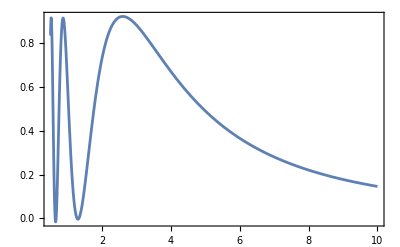

```mathematica
Limit[pmut[s12,c12,s13,c13,c23,s23,dcp,dm31,dm21,ee,a,0],a->0]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.repNum;
Plot[%,{ee,0.5,10},Frame->True]
```

```mathematica
(* compare with figure 4 of 1904.07265 *)
```

```mathematica
(* the figure above is in vaccum. In Appendix B of the reference above, they discuss that the vacum probability is a good approximation for the energies (above tau threshold)and length involved in DUNE *)
```

```mathematica
pmut[s12,c12,s13,c13,c23,s23,dcp,dm31,dm21,ee,aa,0]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.repNum;
(*vaccum *)
Limit[%,aa->0]/.ee->4.5
(*matter*) 
Limit[%%,aa->10^-4]/.ee->4.5
```

0.572819

0.573139